# H-matrix - 3DT0 elements Checking computational cost scaling

## Load Libraries

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../"]
<<BigWhamLink`
$BigWhamVersion
GetFilesDate[]
<<NDSolve`FEM`
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/}

BigWhamLink`LTemplate`Classes`

1.2.1

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Thu 18 Feb 2021 22:18:06GMT+1,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Thu 18 Feb 2021 20:24:13GMT+1}

## Mesh

```mathematica
(* FUNCTION TO PLOT A MESH *)
Options[PlotMesh]={GraphicsDirective->Opacity[0.1] };
PlotMesh[MeshA_,OptionsPattern[]]:= Graphics3D[{ OptionValue[GraphicsDirective],Polygon[MeshA["Nodes"][[#]]&/@MeshA["Connectivity"]]}]
```

### Rotation matrices

```mathematica
computeRotationMatrix[y1_List,y2_List,y3_List]:=Module[
{tangent1,normal,tangent2,rotMat},
tangent1=y2-y1;
tangent1=tangent1/Norm[tangent1];
normal=Cross[tangent1,y3-y1];
normal=normal/Norm[normal];
tangent2=Cross[normal,tangent1];
rotMat={tangent1,tangent2,normal}
];
```

```mathematica
GetElementsRotation[meshA_Association]:=Table[
computeRotationMatrix[
meshA["Nodes"][[meshA["Connectivity"][[i,1]]]],
meshA["Nodes"][[meshA["Connectivity"][[i,2]]]],
meshA["Nodes"][[meshA["Connectivity"][[i,3]]]]],
{i,meshA["Nelts"]}];
```

### Mesh NDSolve FEM

```mathematica
(* function to generate a simple 2D MESH of a cohesive crack*)
PlanarFaultEllipticalMesh[BmaxCellMeasure_,maxCellMeasure_,R_,ab_:1]:=Module[{bmesh,mesh,coorOrder1,connOrder1},

bmesh=ToBoundaryMesh[ImplicitRegion[x^2+(y/ab)^2≤R^2,{x,y}],"MeshOrder"->1,"MaxBoundaryCellMeasure"->BmaxCellMeasure,AccuracyGoal->1,MaxCellMeasure->maxCellMeasure];

mesh=ToElementMesh[bmesh,"MeshOrder"->1,"RegionHoles"->None,MaxCellMeasure->maxCellMeasure];
 
coorOrder1=mesh["Coordinates"];
coorOrder1=MapThread[Append,{coorOrder1,ConstantArray[0,Length[coorOrder1]]}];
connOrder1=mesh["MeshElements"][[1]][[1]];

<|"Nodes"-> coorOrder1,"Connectivity"-> connOrder1, "Nelts"-> Length[connOrder1],"Nnodes"-> Length[coorOrder1]|>
];
```

```mathematica
mesh=PlanarFaultEllipticalMesh[0.1,0.01,1,1];
```

```mathematica
PlotMesh[mesh]
```

-Graphics3D-

```mathematica
AllRot=GetElementsRotation[mesh]
```

{{{0.921529,0.388311,0.},{-0.388311,0.921529,0.},{0.,0.,1.}},{{0.969678,0.244388,0.},{-0.244388,0.969678,0.},{0.,0.,1.}},542,{{-0.970558,0.24087,0.},{-0.24087,-0.970558,0.},{0.,0.,1.}},{{0.838638,-0.544688,0.},{0.544688,0.838638,0.},{0.,0.,1.}}}
 |  |  |  |

## H-mat functions utilities

```mathematica
Options[ConstructHmat]={"Max leaf size"-> 100,"η"-> 3,"ϵ aca"-> 10.^-4};
ConstructHmat[meshA_,kernel_,prop_,OptionsPattern[]]:=  
(* no checks just API embedding here ;( *)
toHMatExpr[meshA["Nodes"],meshA["Connectivity"],kernel,prop,OptionValue["Max leaf size"],OptionValue["η"],OptionValue["ϵ aca"]]
```

```mathematica
h1=ConstructHmat[mesh,"3DT0",{1.,0.3}];//AbsoluteTiming
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

{0.90822,Null}

```mathematica
GetHdotTiming[h_,hdotF_]:=Module[{x,ndof,tt,y},
ndof=GetSize[h][[2]];
x=RandomReal[{-1,1},ndof ];
tt=((y=hdotF[h,x];)//RepeatedTiming)[[1]];
{ndof,tt}
]
```

```mathematica
GetHdotTiming[h1,Hdot]
```

{1638,0.000697499}

```mathematica
GetHdotTiming[h1,HdotRec]
```

{1638,0.000354659}

```mathematica
GetCompressionRatio[h1]
GetSize[h1]
```

0.79515

{1638,1638}

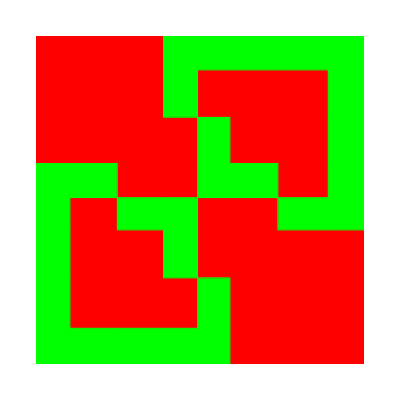

```mathematica
PlotHpattern[h1]
```

## check scalings

0.316228

```mathematica
getStats[Nx_]:=Module[{mesh,thmat,h1,hdt,ndof,cr,hdrect},
mesh=PlanarFaultEllipticalMesh[0.1,0.1 /Nx,1,1];
thmat=(h1=ConstructHmat[mesh,"3DT0",{1.,0.3}];//AbsoluteTiming)[[1]];
hdt=GetHdotTiming[h1,Hdot];
hdrect=GetHdotTiming[h1,HdotRec];
ndof=GetSize[h1][[2]];
cr=GetCompressionRatio[h1];h1=.;
{ndof,cr,thmat,hdt[[2]],hdrect[[2]]}
]
```

```mathematica
res=getStats[#]& /@{5,10,50,100,500}
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

{{1050,1.,0.381118,0.000250584,0.0000988843},{1638,0.79515,0.881308,0.000699283,0.000372054},{7434,0.398812,10.0844,0.0107938,0.0120038},{15000,0.247376,28.0812,0.0171953,0.0282761},{74364,0.0710355,234.724,0.122631,0.203187}}

```mathematica
res//Dimensions
```

{5,5}

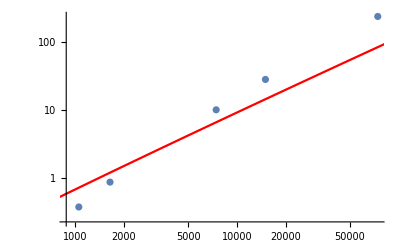

```mathematica
Show[ListLogLogPlot[res[[;;,{1,3}]]],LogLogPlot[ .0001  n Log[n],{n,10,100000},PlotStyle->Red]]
```

```mathematica
res[[;;,{1,5}]]
```

{{1050,0.0000988843},{1638,0.000372054},{7434,0.0120038},{15000,0.0282761},{74364,0.203187}}

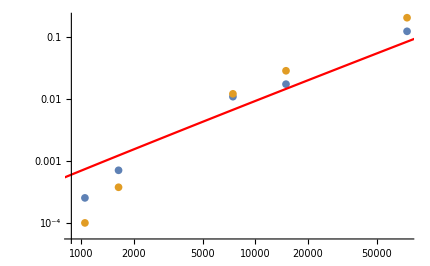

```mathematica
Show[ListLogLogPlot[{res[[;;,{1,4}]],res[[;;,{1,5}]]}],LogLogPlot[ .0000001  n Log[n],{n,10,100000},PlotStyle->Red]]
```